## Finding Positive trees

```mathematica
trees2=Table[
Block[{candidates,candidates2},
candidates= Select[
Keys[allGraphs5],
allGraphs5[#,"vertexsets"]==vs&& 
With[{g=allGraphs5[#,"graph"]},
VertexCount[g]==Length[vs]&&
ConnectedGraphQ[g] &&
PathGraphQ[g] &&
EdgeCount[g]==Length[vs]-1]&];
If[Length[candidates]==1,
First[candidates],
candidates2=Select[candidates,ToString[allGraphs5[#,"comp"]]≠"GreaterEqual"&];
If[Length[candidates2]>0,
First[candidates2],
Print["Failed for ",vs , "."]
]
]
]
,{vs,partitions}];Length[trees2]
```

52

```mathematica
Table[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],{k,trees2}]
```

{-Graphics-26328,-Graphics-26354,-Graphics-27060,-Graphics-28476,-Graphics-29186,-Graphics-27109,-Graphics-29232,-Graphics-28621,-Graphics-29328,-Graphics-29378,-Graphics-28947,-Graphics-29648,-Graphics-29706,-Graphics-29826,-Graphics-29888,-Graphics-27813,-Graphics-29938,-Graphics-30082,-Graphics-30406,-Graphics-30586,-Graphics-30735,-Graphics-24414,-Graphics-11244,-Graphics-31924,-Graphics-31984,-Graphics-32198,-Graphics-32684,-Graphics-35271,-Graphics-35978,-Graphics-15454,-Graphics-14044,-Graphics-36194,-Graphics-36736,-Graphics-36898,-Graphics-38254,-Graphics-38308,-Graphics-39014,-Graphics-48441,-Graphics-49196,-Graphics-49200,-Graphics-49212,-Graphics-49220,-Graphics-49954,-Graphics-49972,-Graphics-51472,-Graphics-51478,-Graphics-52232,-Graphics-56010,-Graphics-56012,-Graphics-56770,-Graphics-58288,-Graphics-59048}

```mathematica
PathGraphQ
```

PathGraphQ

```mathematica
allGraphs5[0,"comp"]
```

Greater

```mathematica
PartitionToSymbol3[part_]:=Block[{end},
end=StringRiffle[Map[SetToString[#]&,Sort[part,Min[#1]<Min[#2]&]],"x"];
Symbol["t"<>end]]
```

```mathematica
treeSyms2=Sort[Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]],{k,trees2}],CompareSymbols]
```

{t1x2x3x4x5,t1x2x3x45,t1x2x34x5,t1x2x35x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x45,t1x24x35,t1x25x34,t12x3x45,t12x34x5,t12x35x4,t13x2x45,t13x24x5,t13x25x4,t14x2x35,t14x23x5,t14x25x3,t15x2x34,t15x23x4,t15x24x3,t1x2x345,t1x234x5,t1x235x4,t1x245x3,t123x4x5,t124x3x5,t125x3x4,t134x2x5,t135x2x4,t145x2x3,t12x345,t123x45,t124x35,t125x34,t13x245,t134x25,t135x24,t14x235,t145x23,t15x234,t1x2345,t1234x5,t1235x4,t1245x3,t1345x2,t12345}

```mathematica
treeRep2=Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]]->Tooltip[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],allGraphs5[k,"compwhy"]],{k,trees2}]
```

{t1x2x3x4x5→-Graphics-26328,t1x2x3x45→-Graphics-26354,t1x2x35x4→-Graphics-27060,t1x2x34x5→-Graphics-28476,t1x2x345→-Graphics-29186,t1x25x3x4→-Graphics-27109,t1x25x34→-Graphics-29232,t1x24x3x5→-Graphics-28621,t1x24x35→-Graphics-29328,t1x245x3→-Graphics-29378,t1x23x4x5→-Graphics-28947,t1x23x45→-Graphics-29648,t1x235x4→-Graphics-29706,t1x234x5→-Graphics-29826,t1x2345→-Graphics-29888,t15x2x3x4→-Graphics-27813,t15x2x34→-Graphics-29938,t15x24x3→-Graphics-30082,t15x23x4→-Graphics-30406,t15x234→-Graphics-30586,t14x2x3x5→-Graphics-30735,t14x2x35→-Graphics-24414,t14x25x3→-Graphics-11244,t14x23x5→-Graphics-31924,t14x235→-Graphics-31984,t145x2x3→-Graphics-32198,t145x23→-Graphics-32684,t13x2x4x5→-Graphics-35271,t13x2x45→-Graphics-35978,t13x25x4→-Graphics-15454,t13x24x5→-Graphics-14044,t13x245→-Graphics-36194,t135x2x4→-Graphics-36736,t135x24→-Graphics-36898,t134x2x5→-Graphics-38254,t134x25→-Graphics-38308,t1345x2→-Graphics-39014,t12x3x4x5→-Graphics-48441,t12x3x45→-Graphics-49196,t12x35x4→-Graphics-49200,t12x34x5→-Graphics-49212,t12x345→-Graphics-49220,t125x3x4→-Graphics-49954,t125x34→-Graphics-49972,t124x3x5→-Graphics-51472,t124x35→-Graphics-51478,t1245x3→-Graphics-52232,t123x4x5→-Graphics-56010,t123x45→-Graphics-56012,t1235x4→-Graphics-56770,t1234x5→-Graphics-58288,t12345→-Graphics-59048}

```mathematica
mat2=Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]]==allGraphs5[k,"colofour"],{k,trees2}];TableForm[mat2]
```

t1x2x3x4x5==v145x23+v145x2x3+v14x23x5+v14x25x3+v14x2x3x5+v15x23x4+v15x2x34+v15x2x3x4+v1x23x45+v1x23x4x5+v1x25x34+v1x25x3x4+v1x2x34x5+v1x2x3x45+v1x2x3x4x5
t1x2x3x45==v145x23+v145x2x3+v1x23x45+v1x2x345+v1x2x3x45
t1x2x35x4==v14x235+v14x2x35+v1x235x4+v1x2x345+v1x2x35x4
t1x2x34x5==v15x234+v15x2x34+v1x234x5+v1x2x345+v1x2x34x5
t1x2x345==v1x2345+v1x2x345
t1x25x3x4==v14x235+v14x25x3+v1x235x4+v1x25x34+v1x25x3x4
t1x25x34==v1x2345+v1x25x34
t1x24x3x5==v15x234+v15x24x3+v1x234x5+v1x24x35+v1x24x3x5
t1x24x35==v1x2345+v1x24x35
t1x245x3==v1x2345+v1x245x3
t1x23x4x5==v15x234+v15x23x4+v1x234x5+v1x23x45+v1x23x4x5
t1x23x45==v1x2345+v1x23x45
t1x235x4==v1x2345+v1x235x4
t1x234x5==v1x2345+v1x234x5
t1x2345==v1x2345
t15x2x3x4==v145x23+v145x2x3+v15x23x4+v15x2x34+v15x2x3x4
t15x2x34==v15x234+v15x2x34
t15x24x3==v15x234+v15x24x3
t15x23x4==v15x234+v15x23x4
t15x234==v15x234
t14x2x3x5==v145x23+v145x2x3+v14x23x5+v14x2x35+v14x2x3x5
t14x2x35==v1345x2+v14x2x35
t14x25x3==v1245x3+v14x25x3
t14x23x5==v14x235+v14x23x5
t14x235==v14x235
t145x2x3==v145x23+v145x2x3
t145x23==v145x23
t13x2x4x5==v135x24+v135x2x4+v13x24x5+v13x2x45+v13x2x4x5
t13x2x45==v13x245+v13x2x45
t13x25x4==v1235x4+v13x25x4
t13x24x5==v1234x5+v13x24x5
t13x245==v13x245
t135x2x4==v135x24+v135x2x4
t135x24==v135x24
t134x2x5==v134x25+v134x2x5
t134x25==v134x25
t1345x2==v1345x2
t12x3x4x5==v125x34+v125x3x4+v12x34x5+v12x3x45+v12x3x4x5
t12x3x45==v12x345+v12x3x45
t12x35x4==v12x345+v12x35x4
t12x34x5==v12x345+v12x34x5
t12x345==v12x345
t125x3x4==v125x34+v125x3x4
t125x34==v125x34
t124x3x5==v124x35+v124x3x5
t124x35==v124x35
t1245x3==v1245x3
t123x4x5==v123x45+v123x4x5
t123x45==v123x45
t1235x4==v1235x4
t1234x5==v1234x5
t12345==v12345

```mathematica
sols2=First[Solve[mat2,syms]]
```

{v1x2x3x4x5→-t1345x2+2 t145x2x3+t14x235+t14x2x35-t14x2x3x5+t15x23x4+t15x2x34-t15x2x3x4-6 t1x2345+2 t1x234x5+t1x235x4+t1x23x45-t1x23x4x5-t1x25x3x4+2 t1x2x345-t1x2x34x5-t1x2x3x45+t1x2x3x4x5,v1x2x3x45→-t145x2x3+2 t1x2345-t1x23x45-t1x2x345+t1x2x3x45,v1x2x35x4→t1345x2-t14x235-t14x2x35+2 t1x2345-t1x235x4-t1x2x345+t1x2x35x4,v1x2x34x5→-t15x2x34+2 t1x2345-t1x234x5-t1x2x345+t1x2x34x5,v1x2x345→-t1x2345+t1x2x345,v1x25x3x4→t1245x3-t14x235-t14x25x3+2 t1x2345-t1x235x4-t1x25x34+t1x25x3x4,v1x25x34→-t1x2345+t1x25x34,v1x24x3x5→-t15x24x3+2 t1x2345-t1x234x5-t1x24x35+t1x24x3x5,v1x24x35→-t1x2345+t1x24x35,v1x245x3→-t1x2345+t1x245x3,v1x23x4x5→-t15x23x4+2 t1x2345-t1x234x5-t1x23x45+t1x23x4x5,v1x23x45→-t1x2345+t1x23x45,v1x235x4→-t1x2345+t1x235x4,v1x234x5→-t1x2345+t1x234x5,v1x2345→t1x2345,v15x2x3x4→-t145x2x3+2 t15x234-t15x23x4-t15x2x34+t15x2x3x4,v15x2x34→-t15x234+t15x2x34,v15x24x3→-t15x234+t15x24x3,v15x23x4→-t15x234+t15x23x4,v15x234→t15x234,v14x2x3x5→t1345x2-t145x2x3+t14x235-t14x23x5-t14x2x35+t14x2x3x5,v14x2x35→-t1345x2+t14x2x35,v14x25x3→-t1245x3+t14x25x3,v14x23x5→-t14x235+t14x23x5,v14x235→t14x235,v145x2x3→-t145x23+t145x2x3,v145x23→t145x23,v13x2x4x5→t1234x5-t135x2x4+t13x245-t13x24x5-t13x2x45+t13x2x4x5,v13x2x45→-t13x245+t13x2x45,v13x25x4→-t1235x4+t13x25x4,v13x24x5→-t1234x5+t13x24x5,v13x245→t13x245,v135x2x4→-t135x24+t135x2x4,v135x24→t135x24,v134x2x5→-t134x25+t134x2x5,v134x25→t134x25,v1345x2→t1345x2,v12x3x4x5→-t125x3x4+2 t12x345-t12x34x5-t12x3x45+t12x3x4x5,v12x3x45→-t12x345+t12x3x45,v12x35x4→-t12x345+t12x35x4,v12x34x5→-t12x345+t12x34x5,v12x345→t12x345,v125x3x4→-t125x34+t125x3x4,v125x34→t125x34,v124x3x5→-t124x35+t124x3x5,v124x35→t124x35,v1245x3→t1245x3,v123x4x5→-t123x45+t123x4x5,v123x45→t123x45,v1235x4→t1235x4,v1234x5→t1234x5,v12345→t12345}

```mathematica
repAlfas=Table[TraditionalForm[(allGraphs5[k,"colofour"]/.sols2)]==0,{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]
```

{t13x24x5-t1234x5==0,t14x25x3-t1245x3==0,t1x24x35-t1x2345==0,t13x25x4-t1235x4==0,t14x2x35-t1345x2==0}

```mathematica
TableForm[
Table[
Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]->
{allGraphs5[k,"colofour"]/.sols2/.treeRep2,allGraphs5[k,"colofour"]/.sols2},
{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}
]
]
```

-Graphics-36166→{--Graphics-58288+-Graphics-14044,-t1234x5+t13x24x5}
-Graphics-31738→{--Graphics-52232+-Graphics-11244,-t1245x3+t14x25x3}
-Graphics-29608→{--Graphics-29888+-Graphics-29328,-t1x2345+t1x24x35}
-Graphics-36112→{--Graphics-56770+-Graphics-15454,-t1235x4+t13x25x4}
-Graphics-31714→{--Graphics-39014+-Graphics-24414,-t1345x2+t14x2x35}
-Graphics-36085→{-Graphics-58288+-Graphics-36194--Graphics-36736--Graphics-35978--Graphics-14044+-Graphics-35271,t1234x5-t135x2x4+t13x245-t13x24x5-t13x2x45+t13x2x4x5}
-Graphics-29605→{2 -Graphics-29888--Graphics-29826--Graphics-30082--Graphics-29328+-Graphics-28621,-t15x24x3+2 t1x2345-t1x234x5-t1x24x35+t1x24x3x5}
-Graphics-29527→{-Graphics-39014+2 -Graphics-29888--Graphics-31984--Graphics-29706--Graphics-29186--Graphics-24414+-Graphics-27060,t1345x2-t14x235-t14x2x35+2 t1x2345-t1x235x4-t1x2x345+t1x2x35x4}
-Graphics-31711→{-Graphics-39014+-Graphics-31984--Graphics-31924--Graphics-32198--Graphics-24414+-Graphics-30735,t1345x2-t145x2x3+t14x235-t14x23x5-t14x2x35+t14x2x3x5}
-Graphics-29551→{-Graphics-52232+2 -Graphics-29888--Graphics-31984--Graphics-29706--Graphics-29232--Graphics-11244+-Graphics-27109,t1245x3-t14x235-t14x25x3+2 t1x2345-t1x235x4-t1x25x34+t1x25x3x4}

```mathematica
Simplify[t1234x5-t135x2x4+t13x245-t13x24x5-t13x2x45+t13x2x4x5>0&&-t1234x5+t13x24x5==0]
```

t1234x5+t13x245+t13x2x4x5>t135x2x4+t13x24x5+t13x2x45&&t1234x5==t13x24x5

```mathematica
t1234x5+t13x245+t13x2x4x5>t135x2x4+t13x24x5+t13x2x45/.treeRep2
```

-Graphics-58288+-Graphics-36194+-Graphics-35271>-Graphics-36736+-Graphics-35978+-Graphics-14044

```mathematica
TableForm[
Table[
Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]]->((allGraphs5[k,"colofour"]/.sols2)/.repAlfas/.treeRep2),
{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key,quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}
]
]
```

ReplaceAll::reps: {t13x24x5-t1234x5==0,t14x25x3-t1245x3==0,t1x24x35-t1x2345==0,t13x25x4-t1235x4==0,t14x2x35-t1345x2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: … is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {t13x24x5-t1234x5==0,t14x25x3-t1245x3==0,t1x24x35-t1x2345==0,t13x25x4-t1235x4==0,t14x2x35-t1345x2==0} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-36166→(--Graphics-58288+-Graphics-14044/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-31738→(--Graphics-52232+-Graphics-11244/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-29608→(--Graphics-29888+-Graphics-29328/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-36112→(--Graphics-56770+-Graphics-15454/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-31714→(--Graphics-39014+-Graphics-24414/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-36085→(-Graphics-58288+-Graphics-36194--Graphics-36736--Graphics-35978--Graphics-14044+-Graphics-35271/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-29605→(2 -Graphics-29888--Graphics-29826--Graphics-30082--Graphics-29328+-Graphics-28621/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-29527→(-Graphics-39014+2 -Graphics-29888--Graphics-31984--Graphics-29706--Graphics-29186--Graphics-24414+-Graphics-27060/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-31711→(-Graphics-39014+-Graphics-31984--Graphics-31924--Graphics-32198--Graphics-24414+-Graphics-30735/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})
-Graphics-29551→(-Graphics-52232+2 -Graphics-29888--Graphics-31984--Graphics-29706--Graphics-29232--Graphics-11244+-Graphics-27109/.{-Graphics-14044--Graphics-58288==0,-Graphics-11244--Graphics-52232==0,-Graphics-29328--Graphics-29888==0,-Graphics-15454--Graphics-56770==0,-Graphics-24414--Graphics-39014==0})

```mathematica
ExpressionToTable2[
Reduce[
Join[
Table[
(allGraphs5[k,"colofour"]/.sols2)==0,
{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}
],
Table[
(allGraphs5[k,"colofour"]/.sols2)>0,
{k,{quad1Key,quad2Key,quad3Key,quad4Key,quad5Key}}
]



]
]
]/.treeRep2
```

SymbolName::sym: Argument t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4 at position 1 is expected to be a symbol.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1].

SymbolName::sym: Argument t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4 at position 1 is expected to be a symbol.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1],3,0] is not a list of digits or a string of valid digits.

StringJoin::string: String expected at position 1 in StringJoin[t5x4∈Rals].

SymbolName::sym: Argument t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4 at position 1 is expected to be a symbol.

General::stop: Further output of SymbolName::sym will be suppressed during this calculation.

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1].

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1].

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1],3,0].

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1],3,0] is not a list of digits or a string of valid digits.

StringJoin::string: String expected at position 1 in StringJoin[t5x4∈Rals].

StringTake::strse: String or list of strings expected at position 1 in StringTake[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1].

General::stop: Further output of StringTake::strse will be suppressed during this calculation.

StringDrop::strse: String or list of strings expected at position 1 in StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1].

General::stop: Further output of StringDrop::strse will be suppressed during this calculation.

StringPadLeft::strse: String or list of strings expected at position 1 in StringPadLeft[StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1],3,0].

General::stop: Further output of StringPadLeft::strse will be suppressed during this calculation.

FromDigits::nlst: The expression StringPadLeft[StringDrop[SymbolName[t13x245|t13x24x5|t13x2x45|t13x2x4x5|t14x23x5|t14x25x3|t14x2x35|t14x2x3x5|t1x234x5|t1x235x4|t1x24x35|t1x24x3x5|t1x25x3x4|t1x2x345|t1x2x35x4],1],3,0] is not a list of digits or a string of valid digits.

General::stop: Further output of FromDigits::nlst will be suppressed during this calculation.

StringJoin::string: String expected at position 1 in StringJoin[t5x4∈Rals].

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

-Graphics-29888==-Graphics-29328
-Graphics-58288==-Graphics-14044
-Graphics-39014==-Graphics-24414
-Graphics-52232==-Graphics-11244
-Graphics-56770==-Graphics-15454
(-Graphics-36194|-Graphics-14044|-Graphics-35978|-Graphics-35271|-Graphics-31924|-Graphics-11244|-Graphics-24414|-Graphics-30735|-Graphics-29826|-Graphics-29706|-Graphics-29328|-Graphics-28621|-Graphics-27109|-Graphics-29186|-Graphics-27060)∈Reals
-Graphics-31924+-Graphics-32198<-Graphics-31984+-Graphics-30735
-Graphics-36736+-Graphics-35978<-Graphics-36194+-Graphics-35271
-Graphics-29826+-Graphics-30082<-Graphics-29328+-Graphics-28621
-Graphics-31984+-Graphics-29706+-Graphics-29186<2 -Graphics-29328+-Graphics-27060
-Graphics-31984+-Graphics-29706+-Graphics-29232<2 -Graphics-29328+-Graphics-27109

## Now for real null colofour

```mathematica
mat3=Table[PartitionToSymbol3[allGraphs5[k,"vertexsets"]]==allGraphs5[k,"colofourrealnull"],{k,trees2}];TableForm[mat3]
```

t1x2x3x4x5==n12345-n1234x5-n1235x4+n123x4x5-n124x35+n124x3x5+n12x35x4-n12x3x4x5-n135x24+n135x2x4+n13x24x5-n13x2x4x5+n1x24x35-n1x24x3x5-n1x2x35x4+n1x2x3x4x5
t1x2x3x45==-n12345+n123x45+n1245x3-n12x3x45+n13x245-n13x2x45-n1x245x3+n1x2x3x45
t1x2x35x4==-n12345+n1235x4+n124x35-n12x35x4+n135x24-n135x2x4-n1x24x35+n1x2x35x4
t1x2x34x5==-n12345+n1234x5+n125x34-n12x34x5+n134x25-n134x2x5-n1x25x34+n1x2x34x5
t1x2x345==n12345-n12x345-n1345x2+n1x2x345
t1x25x3x4==-n12345+n1235x4+n1245x3-n125x3x4+n13x245-n13x25x4-n1x245x3+n1x25x3x4
t1x25x34==n12345-n125x34-n134x25+n1x25x34
t1x24x3x5==-n12345+n1234x5+n1245x3-n124x3x5+n13x245-n13x24x5-n1x245x3+n1x24x3x5
t1x24x35==n12345-n124x35-n135x24+n1x24x35
t1x245x3==n12345-n1245x3-n13x245+n1x245x3
t1x23x4x5==-n12345+n1234x5+n1235x4-n123x4x5+n14x235-n14x23x5-n1x235x4+n1x23x4x5
t1x23x45==n12345-n123x45-n145x23+n1x23x45
t1x235x4==n12345-n1235x4-n14x235+n1x235x4
t1x234x5==n12345-n1234x5-n15x234+n1x234x5
t1x2345==-n12345+n1x2345
t15x2x3x4==-n12345+n1235x4+n1245x3-n125x3x4+n135x24-n135x2x4-n15x24x3+n15x2x3x4
t15x2x34==n12345-n125x34-n1345x2+n15x2x34
t15x24x3==n12345-n1245x3-n135x24+n15x24x3
t15x23x4==n12345-n1235x4-n145x23+n15x23x4
t15x234==-n12345+n15x234
t14x2x3x5==-n12345+n1234x5+n1245x3-n124x3x5+n134x25-n134x2x5-n14x25x3+n14x2x3x5
t14x2x35==n12345-n124x35-n14x235+n14x2x35
t14x25x3==n12345-n134x25-n14x235+n14x25x3
t14x23x5==n12345-n1234x5-n145x23+n14x23x5
t14x235==-n12345+n14x235
t145x2x3==n12345-n1245x3-n1345x2+n145x2x3
t145x23==-n12345+n145x23
t13x2x4x5==-n12345+n1234x5+n1235x4-n123x4x5+n134x25-n134x2x5-n13x25x4+n13x2x4x5
t13x2x45==n12345-n123x45-n1345x2+n13x2x45
t13x25x4==n12345-n134x25-n13x245+n13x25x4
t13x24x5==n12345-n135x24-n13x245+n13x24x5
t13x245==-n12345+n13x245
t135x2x4==n12345-n1235x4-n1345x2+n135x2x4
t135x24==-n12345+n135x24
t134x2x5==n12345-n1234x5-n1345x2+n134x2x5
t134x25==-n12345+n134x25
t1345x2==-n12345+n1345x2
t12x3x4x5==-n12345+n1234x5+n1235x4-n123x4x5+n124x35-n124x3x5-n12x35x4+n12x3x4x5
t12x3x45==n12345-n123x45-n1245x3+n12x3x45
t12x35x4==n12345-n1235x4-n124x35+n12x35x4
t12x34x5==n12345-n1234x5-n125x34+n12x34x5
t12x345==-n12345+n12x345
t125x3x4==n12345-n1235x4-n1245x3+n125x3x4
t125x34==-n12345+n125x34
t124x3x5==n12345-n1234x5-n1245x3+n124x3x5
t124x35==-n12345+n124x35
t1245x3==-n12345+n1245x3
t123x4x5==n12345-n1234x5-n1235x4+n123x4x5
t123x45==-n12345+n123x45
t1235x4==-n12345+n1235x4
t1234x5==-n12345+n1234x5
t12345==n12345

```mathematica
syms2=Sort[Table[allGraphs5[k,"colofourrealnull"],{k,allGraphs5NullAtomKeys}],CompareSymbols]
```

{n1x2x3x4x5,n1x2x3x45,n1x2x34x5,n1x2x35x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x45,n1x24x35,n1x25x34,n12x3x45,n12x34x5,n12x35x4,n13x2x45,n13x24x5,n13x25x4,n14x2x35,n14x23x5,n14x25x3,n15x2x34,n15x23x4,n15x24x3,n1x2x345,n1x234x5,n1x235x4,n1x245x3,n123x4x5,n124x3x5,n125x3x4,n134x2x5,n135x2x4,n145x2x3,n12x345,n123x45,n124x35,n125x34,n13x245,n134x25,n135x24,n14x235,n145x23,n15x234,n1x2345,n1234x5,n1235x4,n1245x3,n1345x2,n12345}

```mathematica
sols3=First[Solve[mat3,syms2]]
```

{n1x2x3x4x5→t12345+t1234x5+t123x4x5+t1245x3+t124x3x5+t12x35x4+t12x3x4x5+t1345x2+t134x2x5+t13x245+t13x25x4+t13x2x4x5+t1x245x3+t1x24x3x5+t1x2x35x4+t1x2x3x4x5,n1x2x3x45→t12345+t123x45+t1245x3+t12x3x45+t1345x2+t13x2x45+t1x245x3+t1x2x3x45,n1x2x34x5→t12345+t1234x5+t125x34+t12x34x5+t1345x2+t134x2x5+t1x25x34+t1x2x34x5,n1x2x35x4→t12345+t1235x4+t124x35+t12x35x4+t1345x2+t135x2x4+t1x24x35+t1x2x35x4,n1x23x4x5→t12345+t1234x5+t1235x4+t123x4x5+t145x23+t14x23x5+t1x235x4+t1x23x4x5,n1x24x3x5→t12345+t1245x3+t124x3x5+t135x24+t13x245+t13x24x5+t1x245x3+t1x24x3x5,n1x25x3x4→t12345+t1245x3+t125x3x4+t134x25+t13x245+t13x25x4+t1x245x3+t1x25x3x4,n12x3x4x5→t12345+t1234x5+t1235x4+t123x4x5+t1245x3+t124x3x5+t12x35x4+t12x3x4x5,n13x2x4x5→t12345+t1234x5+t123x4x5+t1345x2+t134x2x5+t13x245+t13x25x4+t13x2x4x5,n14x2x3x5→t12345+t1234x5+t124x3x5+t1345x2+t134x2x5+t14x235+t14x25x3+t14x2x3x5,n15x2x3x4→t12345+t1235x4+t1245x3+t125x3x4+t1345x2+t135x2x4+t15x24x3+t15x2x3x4,n1x23x45→t12345+t123x45+t145x23+t1x23x45,n1x24x35→t12345+t124x35+t135x24+t1x24x35,n1x25x34→t12345+t125x34+t134x25+t1x25x34,n12x3x45→t12345+t123x45+t1245x3+t12x3x45,n12x34x5→t12345+t1234x5+t125x34+t12x34x5,n12x35x4→t12345+t1235x4+t124x35+t12x35x4,n13x2x45→t12345+t123x45+t1345x2+t13x2x45,n13x24x5→t12345+t135x24+t13x245+t13x24x5,n13x25x4→t12345+t134x25+t13x245+t13x25x4,n14x2x35→t12345+t124x35+t14x235+t14x2x35,n14x23x5→t12345+t1234x5+t145x23+t14x23x5,n14x25x3→t12345+t134x25+t14x235+t14x25x3,n15x2x34→t12345+t125x34+t1345x2+t15x2x34,n15x23x4→t12345+t1235x4+t145x23+t15x23x4,n15x24x3→t12345+t1245x3+t135x24+t15x24x3,n1x2x345→t12345+t12x345+t1345x2+t1x2x345,n1x234x5→t12345+t1234x5+t15x234+t1x234x5,n1x235x4→t12345+t1235x4+t14x235+t1x235x4,n1x245x3→t12345+t1245x3+t13x245+t1x245x3,n123x4x5→t12345+t1234x5+t1235x4+t123x4x5,n124x3x5→t12345+t1234x5+t1245x3+t124x3x5,n125x3x4→t12345+t1235x4+t1245x3+t125x3x4,n134x2x5→t12345+t1234x5+t1345x2+t134x2x5,n135x2x4→t12345+t1235x4+t1345x2+t135x2x4,n145x2x3→t12345+t1245x3+t1345x2+t145x2x3,n12x345→t12345+t12x345,n123x45→t12345+t123x45,n124x35→t12345+t124x35,n125x34→t12345+t125x34,n13x245→t12345+t13x245,n134x25→t12345+t134x25,n135x24→t12345+t135x24,n14x235→t12345+t14x235,n145x23→t12345+t145x23,n15x234→t12345+t15x234,n1x2345→t12345+t1x2345,n1234x5→t12345+t1234x5,n1235x4→t12345+t1235x4,n1245x3→t12345+t1245x3,n1345x2→t12345+t1345x2,n12345→t12345}

```mathematica
nullRep=Table[allGraphs5[k,"colofourrealnull"]->Tooltip[Labeled[allGraphs5[k,"graph"],Style[k,ColourForKey[allGraphs5,k]]],allGraphs5[k,"compwhy"]],{k,allGraphs5NullAtomKeys}];
```

```mathematica
sols3/.treeRep2/.nullRep//TableForm
```

-Graphics-0→-Graphics-59048+-Graphics-58288+-Graphics-52232+-Graphics-39014+-Graphics-36194+-Graphics-56010+-Graphics-51472+-Graphics-49200+-Graphics-38254+-Graphics-29378+-Graphics-15454+-Graphics-48441+-Graphics-35271+-Graphics-28621+-Graphics-27060+-Graphics-26328
-Graphics-2→-Graphics-59048+-Graphics-56012+-Graphics-52232+-Graphics-39014+-Graphics-49196+-Graphics-35978+-Graphics-29378+-Graphics-26354
-Graphics-18→-Graphics-59048+-Graphics-58288+-Graphics-49972+-Graphics-39014+-Graphics-49212+-Graphics-38254+-Graphics-29232+-Graphics-28476
-Graphics-6→-Graphics-59048+-Graphics-56770+-Graphics-51478+-Graphics-39014+-Graphics-49200+-Graphics-36736+-Graphics-29328+-Graphics-27060
-Graphics-486→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-32684+-Graphics-56010+-Graphics-31924+-Graphics-29706+-Graphics-28947
-Graphics-162→-Graphics-59048+-Graphics-52232+-Graphics-36898+-Graphics-36194+-Graphics-51472+-Graphics-29378+-Graphics-14044+-Graphics-28621
-Graphics-54→-Graphics-59048+-Graphics-52232+-Graphics-36194+-Graphics-38308+-Graphics-49954+-Graphics-29378+-Graphics-15454+-Graphics-27109
-Graphics-39366→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-52232+-Graphics-56010+-Graphics-51472+-Graphics-49200+-Graphics-48441
-Graphics-13122→-Graphics-59048+-Graphics-58288+-Graphics-39014+-Graphics-36194+-Graphics-56010+-Graphics-38254+-Graphics-15454+-Graphics-35271
-Graphics-4374→-Graphics-59048+-Graphics-58288+-Graphics-39014+-Graphics-31984+-Graphics-51472+-Graphics-38254+-Graphics-11244+-Graphics-30735
-Graphics-1458→-Graphics-59048+-Graphics-56770+-Graphics-52232+-Graphics-39014+-Graphics-49954+-Graphics-36736+-Graphics-30082+-Graphics-27813
-Graphics-488→-Graphics-59048+-Graphics-56012+-Graphics-32684+-Graphics-29648
-Graphics-168→-Graphics-59048+-Graphics-51478+-Graphics-36898+-Graphics-29328
-Graphics-72→-Graphics-59048+-Graphics-49972+-Graphics-38308+-Graphics-29232
-Graphics-39368→-Graphics-59048+-Graphics-56012+-Graphics-52232+-Graphics-49196
-Graphics-39384→-Graphics-59048+-Graphics-58288+-Graphics-49972+-Graphics-49212
-Graphics-39372→-Graphics-59048+-Graphics-56770+-Graphics-51478+-Graphics-49200
-Graphics-13124→-Graphics-59048+-Graphics-56012+-Graphics-39014+-Graphics-35978
-Graphics-13284→-Graphics-59048+-Graphics-36898+-Graphics-36194+-Graphics-14044
-Graphics-13176→-Graphics-59048+-Graphics-36194+-Graphics-38308+-Graphics-15454
-Graphics-4380→-Graphics-59048+-Graphics-51478+-Graphics-31984+-Graphics-24414
-Graphics-4860→-Graphics-59048+-Graphics-58288+-Graphics-32684+-Graphics-31924
-Graphics-4428→-Graphics-59048+-Graphics-31984+-Graphics-38308+-Graphics-11244
-Graphics-1476→-Graphics-59048+-Graphics-49972+-Graphics-39014+-Graphics-29938
-Graphics-1944→-Graphics-59048+-Graphics-56770+-Graphics-32684+-Graphics-30406
-Graphics-1620→-Graphics-59048+-Graphics-52232+-Graphics-36898+-Graphics-30082
-Graphics-26→-Graphics-59048+-Graphics-49220+-Graphics-39014+-Graphics-29186
-Graphics-666→-Graphics-59048+-Graphics-58288+-Graphics-30586+-Graphics-29826
-Graphics-546→-Graphics-59048+-Graphics-56770+-Graphics-31984+-Graphics-29706
-Graphics-218→-Graphics-59048+-Graphics-52232+-Graphics-36194+-Graphics-29378
-Graphics-52974→-Graphics-59048+-Graphics-58288+-Graphics-56770+-Graphics-56010
-Graphics-43902→-Graphics-59048+-Graphics-58288+-Graphics-52232+-Graphics-51472
-Graphics-40878→-Graphics-59048+-Graphics-56770+-Graphics-52232+-Graphics-49954
-Graphics-17514→-Graphics-59048+-Graphics-58288+-Graphics-39014+-Graphics-38254
-Graphics-14586→-Graphics-59048+-Graphics-56770+-Graphics-39014+-Graphics-36736
-Graphics-5834→-Graphics-59048+-Graphics-52232+-Graphics-39014+-Graphics-32198
-Graphics-39392→-Graphics-59048+-Graphics-49220
-Graphics-52976→-Graphics-59048+-Graphics-56012
-Graphics-43908→-Graphics-59048+-Graphics-51478
-Graphics-40896→-Graphics-59048+-Graphics-49972
-Graphics-13340→-Graphics-59048+-Graphics-36194
-Graphics-17568→-Graphics-59048+-Graphics-38308
-Graphics-14748→-Graphics-59048+-Graphics-36898
-Graphics-4920→-Graphics-59048+-Graphics-31984
-Graphics-6320→-Graphics-59048+-Graphics-32684
-Graphics-2124→-Graphics-59048+-Graphics-30586
-Graphics-728→-Graphics-59048+-Graphics-29888
-Graphics-57528→-Graphics-59048+-Graphics-58288
-Graphics-54492→-Graphics-59048+-Graphics-56770
-Graphics-45416→-Graphics-59048+-Graphics-52232
-Graphics-18980→-Graphics-59048+-Graphics-39014
-Graphics-59048→-Graphics-59048

```mathematica
treeSyms2
```

{t1x2x3x4x5,t1x2x3x45,t1x2x34x5,t1x2x35x4,t1x23x4x5,t1x24x3x5,t1x25x3x4,t12x3x4x5,t13x2x4x5,t14x2x3x5,t15x2x3x4,t1x23x45,t1x24x35,t1x25x34,t12x3x45,t12x34x5,t12x35x4,t13x2x45,t13x24x5,t13x25x4,t14x2x35,t14x23x5,t14x25x3,t15x2x34,t15x23x4,t15x24x3,t1x2x345,t1x234x5,t1x235x4,t1x245x3,t123x4x5,t124x3x5,t125x3x4,t134x2x5,t135x2x4,t145x2x3,t12x345,t123x45,t124x35,t125x34,t13x245,t134x25,t135x24,t14x235,t145x23,t15x234,t1x2345,t1234x5,t1235x4,t1245x3,t1345x2,t12345}

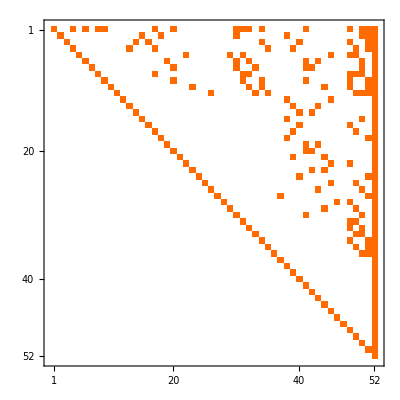

```mathematica
treemat=Map[
Table[Coefficient[#[[2]],t],{t,treeSyms2}]&,
sols3];MatrixPlot[treemat]
```

```mathematica
treeSyms2[[4]]
```

t1x2x35x4

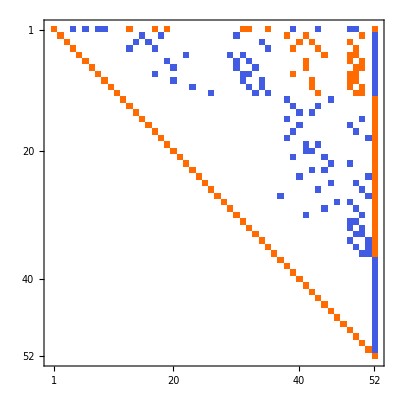

```mathematica
MatrixPlot[Inverse[treemat]]
```